# Chapter 5 - Problem 4

Find the lowest bound state energy for an electron entrapped in the potential described by 
	V(x) = λ_1δ(x+L) + λ_2δ(x) + λ_3δ(x-L/2)
	
where λ_1 =λ_3 = 0.151 eV.nm and λ_2 = 0.01 eV.nm and L = 2 nm

```mathematica
Clear["Global`*"]
(* Constants *)
e = 1.60217 * 10^-19; (* 1 electron volt(ev) = e Joules *)
h = 6.62607004 * 10^-34 ;(* planck's constant *)
m = 9.10938 * 10^-31; (* effective mass of an electron *)
ℏ = h/(2*Pi);
```

```mathematica
(* Given *)
nano = 10^-9;
λ1 = -0.151;
λ2 = -0.01;
λ3 = λ1 ;
L = 2  ;
```

```mathematica
(* k values*)
alphae =Sqrt[(2*m*e)/ℏ^2] * nano; 
k = alphae * Sqrt[en];
k1 = alphae * Sqrt[en - λ1/a];
k2 = alphae * Sqrt[en - λ2/a];
k3 = alphae * Sqrt[en - λ3/a];
```

```mathematica
PI[kL_,kR_]= MatrixExp[(1/2) * Log[kL/kR] * ( PauliMatrix[1] - IdentityMatrix[2])];
PP [kx_,l_] = MatrixExp[-I * kx * l * PauliMatrix[3]]; 
Pdelta[λ_] = {{1 + (I*λ*alphae)/(2*Sqrt[en]) , (I*λ*alphae)/(2*Sqrt[en])},{-1 *(I*λ*alphae)/(2*Sqrt[en]) , 1 - (I*λ*alphae)/(2*Sqrt[en])}};
MatrixForm[Pdelta[λ]];
```

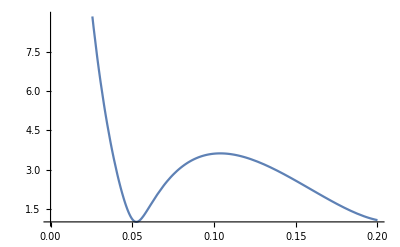

```mathematica
M = Pdelta[λ1].PP[k, L].Pdelta[λ2].PP[k,L/2].Pdelta[λ3];
Plot[Abs[M[[1,1]]],{en,0,0.2}]
```

```mathematica
FindRoot[Abs[M[[1,1]]],{en, 0.05}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{en→-0.150661}